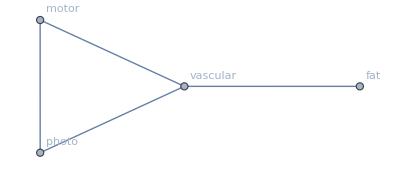

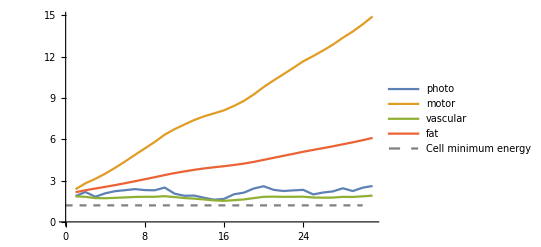

photo | motor | vascular | fat
2.60712 | 14.9204 | 1.91042 | 6.1005

```mathematica
transmitEnergy[c1_,c2_,energy_]:=Module[{},
c1[e]-=energy; 
c2[e]+=energy; 
(*Print[StringForm["e=`` from `` to ``.",energy,c1,c2]];*)
]
exchangeEnergy[c1_,c2_]:=Module[{c1Surp, c2Surp},
c1Surp= Max[c1[e] - (cellMinEnergy) , 0] ;
c2Surp= Max[c1[e] - (cellMinEnergy), 0] ;
transmitEnergy[c1,c2, c1Surp * c1[eOut] * c2[eIn]];
transmitEnergy[c2,c1, c1Surp * c2[eOut] * c1[eIn]];
];
energyStep[]:=Module[{},
photo[e]+=Random[];
exchangeEnergy[photo,vascular];
exchangeEnergy[photo,motor];
exchangeEnergy[vascular,motor];
exchangeEnergy[vascular,fat];
#[e]&/@VertexList[g]
];
cellMinEnergy = 1.2;
photo[eIn]=0.0;
photo[eOut]=0.2;
photo[eMax]=3.0;
photo[e]=2.0;

motor[eIn]=1.0;
motor[eOut]=0.0;
motor[eMax]=3.0;
motor[e]=2.0;

vascular[eIn]=1.0;
vascular[eOut]=0.2;
vascular[eMax]=1.0;
vascular[e]=2.0;

fat[eIn]=1.0;
fat[eOut]=0.01;
fat[eMax]=10.0;
fat[e]=2.0;
g=Graph[{photo<->motor,vascular<->motor,vascular<->fat,photo<->vascular},VertexLabels->"Name"]

nSteps=30;
Show[
ListLinePlot[Transpose[Table[energyStep[],{x,0,nSteps}]],
PlotLegends->VertexList[g]],
Plot[cellMinEnergy,{x,0,nSteps},
PlotStyle->{Dashed,Gray},
PlotLegends->{"Cell minimum energy"}]]
Grid[{VertexList[g],
#[e]&/@VertexList[g]}]
```